# A brief introduction to models of computation

This notebook was prepared by Erik Winfree <winfree@caltech.edu> for Caltech BE/CS 191a, Winter 2022.    Please report any suspected bugs that you encounter!
Do not share this with anyone who is not currently taking the class unless you have permission from Erik Winfree.

## The purpose of this notebook

One of the goals here is to see that simple models of computation can be defined and implemented and explored with ease.  This why the code for doing the simulations is presented.  Although you do not need to decipher and understand the inner workings of the code, you will hopefully appreciate that it is not small enough to be comprehended if you wanted to.  And if you come up with or encounter some other simple model of computation, you ought to feel capable of writing your own simulator in a few lines of code.   When playing with models of computation, don’t just sit there and stew in the juices of your abstract thoughts -- also just try things out!

## Concepts related to models of computation (informally)

Skip this section unless you are interested.

A model (or machine type) : mathematical definition of syntax and semantics.    Example:  Here is how to write down a Boolean logic circuit.   Here is what it does.
A program (or an algorithm):  the specification of a particular machine in a given model.  Could be high-level or low-level depending on the model.
A task (or a problem): a mathematical description of a desired behavior, e.g. given input of a specified form, halt with output that has specified properties.

Uniform versus non-uniform models.  
	Circuits are non-uniform, as you need a larger circuit for larger problem instances.  Turing machines are uniform, as single TM can solve all possible (even infinitely many) instances of a task.
Computability and uncomputability.
	There are well-defined mathematical functions that are uncomputable!  The halting problem and the Busy Beaver problem are well known examples.
Complexity, in terms of time, space, energy, program-size, or other resources.
	Typically considered as worst-case over all inputs of a given size; could also be average case, suitably defined.
	Complexity of a specific algorithm relates to how long that algorithm takes to compute inputs of a given size.
	Complexity of a specific problem relates to what is the best possible complexity over all algorithms (known or unknown) that solve the problem.
Computing functions vs behaviors.
	If one is only interested in the input/output function computed, one considers it to be computed regardless of how long it takes; it just must be correct.
	If one is interested in the response of an algorithm to its environment, one must consider a real-time sequence of inputs and real-time production of outputs.
Simulation and universality.
	One model can simulate another if, for each program in model A, there exists a program in model B that does the same thing, say in terms of input/output function.
	One program, U, in model X is universal for model X if, for each other program P, there is an input p such that U[p,x] = P[x].
	Simulations typically will not preserve running time, e.g. Turing machines can simulate cellular automata in polynomial time, but not in linear time.
	Real-time simulation of behavior, requiring a correspondence to be maintained throughout time, may also be considered... but is conceptually distinct.
Determinism and confluence.
	Local determinism relates to there being exactly one possible next state (or none) for each machine state.
	Non-deterministic models have multiple options; in this class, we will consider semantics where random choices are taken in each “run”. 
	Confluence describes (and generalizes) the situation where the end state is independent of which choices are made.
Reachability and state space.
	Which machine states can be reached from which other machine states? Perhaps more interesting for non-deterministic machines than for deterministic machines.
High-level programming languages and compilers.
	Make it easier to describe desired algorithms!  Translate to a low-level language that is closer to physical implementation.

Models (vaguely) related to Boolean logic circuits:
	Switching circuits.  Combinational circuits.  Sequential circuits.  Relational networks.  Boolean formulas. Finite state machine. Neural networks.
Models (vaguely) related to Turing machines:
	Multi-tape Turing machine.  Multi-head Turing machine.   Stack machines.  Register machines.  Counter machines.
Models (vaguely) related to Random Access Machines (RAM):
	Parallel Random Access Machines (PRAM).  Assembly language.  
Models (vaguely) related to string rewriting systems:.08
	Semi-Thue systems.  Post correspondence problem.  L-systems.  Chomsky’s hierarchy of grammars. Term rewriting systems.
Models (vaguely) related to cellular automata:
	In one dimension, in two dimensions, in three dimensions....  Lattice gas automata.  Ising models.  Turmites and Langton’s ant.   
Models (vaguely) related to asynchronous parallel pointer machines:
	Kolmogorov-Uspenskii machines.  Pointer machines.  Graph grammars.  Graph rewriting systems.  Parallel pointer machines. Schonhage machines.  Wolfram Physics Project.

You may consider the above to be keywords for guiding an internet search for more information.  An excellent textbook is John Savage’s “Models of Computation”.  For models not covered there, I will provide references below.  Some of the models considered here are somewhat non-standard variants, such as the asynchronous gate update semantics for Boolean logic circuits and parallel pointer machines -- strictly speaking, that makes them inequivalent to the standard models for many questions and properties, and you should think of them as having a distinct model name.

## Boolean logic circuits

A Boolean circuit is represented as a list of gates, each expressed as an update rule for the output wire, in terms of free variables representing the values on wires.  The variables must not be defined in Mathematica, so pre-defined symbols like “N” and “C” are off-limits.  However, we make use of Mathematica’s built-in Boolean operators to define the symbolic expressions for each gate.

To represent a circuit, we need to provide names for all the intermediate wires.  The order in which the gates are listed does not matter, but it’s important to appreciate that if circuits are feedforward (i.e. they have no feedback loops) then they are guaranteed to stabilize with final, unchanging values on each wire.  Also note that fanout is an essential feature of circuits -- a computed value gets used more than once.  If a feedforward circuit has no fanout (other than the inputs) then it is a formula.

```mathematica
-Graphics--Graphics-
```

```mathematica
Clear[a,b,c,w1,w2,w3,w4,w5,w6,w7,x,y]; (* it's a good habit to clear symbols that you intend and expect to remain pure and inert symbols *)
```

```mathematica
circ1={x->And[a,b],y->Or[a,Not[x]]}
```

{x→a&&b,y→a||!x}

```mathematica
circ2 ={w1->Not[a],w2->Nand[b,c],w3->And[b,w2],w4->Not[w2],w5->And[w1,w3],w6->Not[w5],w7->Xor[w3,w4],y->Or[w6,w7]}
```

{w1→!a,w2→b⊼c,w3→b&&w2,w4→!w2,w5→w1&&w3,w6→!w5,w7→w3⊻w4,y→w6||w7}

```mathematica
circ3={x->Not[y],y->Not[z],z->Not[x]}
```

{x→!y,y→!z,z→!x}

Our code will allow you to use compound gates, such as x → And[Not[b], Or[c, And[d]]] , if you want to.  However, when discussing circuit size, one must choose a basis set of gates, e.g. AND, OR, NOT, or the 16 2-input gates.

Given a valid circuit, we can extract the full set of wires by analyzing the expression.

```mathematica
CircuitWires[circuit_]:=Union[Flatten[
circuit//.{Rule[wire_,value_]:>{wire,value},(And|Or|Not|Xor|Xnor|Nand|Nor)[args___]:>{args},True|False->{}}]]
```

```mathematica
CircuitWires[circ2]
```

{a,b,c,w1,w2,w3,w4,w5,w6,w7,y}

The dynamics of Boolean circuit operation, for our purposes, will consist of one-at-a-time updates of gates.  It will be useful to know when a circuit is done computing, in the sense that no further updates will change the value of any gate.  To avoid actually assigning values to any of the free variables representing wires (which would wreak havoc with our code), we represent the state of the wires as a list of replacement rules.   Since we are using standard Boolean operators, wire values are True or False, rather than 1 or 0.

```mathematica
CircuitStableQ[circuit_,wirevalues_]:=AllTrue[circuit,(#[[1]]/.wirevalues)===(#[[2]]/.wirevalues)&]
```

```mathematica
CircuitStableQ[circ1,{x->False,a->False,b->False,y->True}]
```

True

```mathematica
CircuitStableQ[circ3,{x->True,y->True,z->True}]
```

False

Circuits are defined using Boolean truth values, True and False, and operators on them.  But sometimes it’s convenient to use 1/0 instead of True/False.  The built-in function Boole converts one way; we define Truth to convert the other way.

```mathematica
{Boole[{True,False,x,True}],Boole[x->True],Boole[{x->False,y->True,z->0}]}//MatrixForm
```

({1,0,Boole[x],1}
x→1
{x→0,y→1,z→Boole[0]})

```mathematica
Truth[0]=False;Truth[1]=True; Attributes[Truth]={Listable};Truth[Rule[LHS_,RHS_]]:=Rule[LHS,Truth[RHS]]
```

```mathematica
{Truth[{1,0,x,1}],Truth[x->1],Truth[{x->0,y->1,z->True}]}//MatrixForm
```

({True,False,Truth[x],True}
x→True
{x→False,y→True,z→Truth[True]})

To evaluate a circuit, given some input, it is natural to evaluate the gates one by one in a feedforward order, until one gets to the output gates.  However, this only works for a feedforward circuit.  As we might be interested in circuits that have recurrent connections, we will instead define a stochastic semantics where we update randomly-chosen gates one at a time until there are no gates that could change.  Thus, depending on the circuit and the input, the computation may be deterministic (not depending on the order of updates), or it may not be, and it may be guaranteed to finish, or it may continue forever.  This method is not efficient, but it gives a “natural” and well-defined semantics. 

We’ll define a “single step” to be repeatedly trying to update gates until one changes.

```mathematica
CircuitStep[circuit_,wirevalues_]:=
Module[{wires=CircuitWires[circuit],state,n},
state=wires/.wirevalues; (* keep a list of wire values, as True/False in order of "wires" *)
If[!CircuitStableQ[circuit,wirevalues],
n=RandomInteger[{1,Length[state]}];(* randomly try gates until one changes *)
While[state[[n]]==(wires[[n]]/.circuit)/.wirevalues,
n=RandomInteger[{1,Length[state]}]];
state[[n]]=(wires[[n]]/.circuit)/.wirevalues
];
MapThread[Rule,{wires,state}]
]
```

```mathematica
circ1
```

{x→a&&b,y→a||!x}

```mathematica
CircuitStep[circ1,{x->False,a->False,b->False,y->True}]
```

{a→False,b→False,x→False,y→True}

```mathematica
FixedPointList[CircuitStep[circ1,#]&,{a->False,b->True,x->True,y->False}]//MatrixForm
```

(a→False | b→True | x→True | y→False
a→False | b→True | x→False | y→False
a→False | b→True | x→False | y→True
a→False | b→True | x→False | y→True)

```mathematica
circ4=Table[x[i]->Not[x[i-1]],{i,1,10}]
```

{x[1]→!x[0],x[2]→!x[1],x[3]→!x[2],x[4]→!x[3],x[5]→!x[4],x[6]→!x[5],x[7]→!x[6],x[8]→!x[7],x[9]→!x[8],x[10]→!x[9]}

```mathematica
FixedPointList[CircuitStep[circ4,#]&,Table[x[i]->(i==0),{i,0,10}]]//Boole//MatrixForm
```

(x[0]→1 | x[1]→0 | x[2]→0 | x[3]→0 | x[4]→0 | x[5]→0 | x[6]→0 | x[7]→0 | x[8]→0 | x[9]→0 | x[10]→0
x[0]→1 | x[1]→0 | x[2]→1 | x[3]→0 | x[4]→0 | x[5]→0 | x[6]→0 | x[7]→0 | x[8]→0 | x[9]→0 | x[10]→0
x[0]→1 | x[1]→0 | x[2]→1 | x[3]→0 | x[4]→0 | x[5]→1 | x[6]→0 | x[7]→0 | x[8]→0 | x[9]→0 | x[10]→0
x[0]→1 | x[1]→0 | x[2]→1 | x[3]→0 | x[4]→0 | x[5]→1 | x[6]→0 | x[7]→0 | x[8]→0 | x[9]→1 | x[10]→0
x[0]→1 | x[1]→0 | x[2]→1 | x[3]→0 | x[4]→1 | x[5]→1 | x[6]→0 | x[7]→0 | x[8]→0 | x[9]→1 | x[10]→0
x[0]→1 | x[1]→0 | x[2]→1 | x[3]→0 | x[4]→1 | x[5]→1 | x[6]→0 | x[7]→1 | x[8]→0 | x[9]→1 | x[10]→0
x[0]→1 | x[1]→0 | x[2]→1 | x[3]→0 | x[4]→1 | x[5]→0 | x[6]→0 | x[7]→1 | x[8]→0 | x[9]→1 | x[10]→0
x[0]→1 | x[1]→0 | x[2]→1 | x[3]→0 | x[4]→1 | x[5]→0 | x[6]→1 | x[7]→1 | x[8]→0 | x[9]→1 | x[10]→0
x[0]→1 | x[1]→0 | x[2]→1 | x[3]→0 | x[4]→1 | x[5]→0 | x[6]→1 | x[7]→0 | x[8]→0 | x[9]→1 | x[10]→0
x[0]→1 | x[1]→0 | x[2]→1 | x[3]→0 | x[4]→1 | x[5]→0 | x[6]→1 | x[7]→0 | x[8]→1 | x[9]→1 | x[10]→0
x[0]→1 | x[1]→0 | x[2]→1 | x[3]→0 | x[4]→1 | x[5]→0 | x[6]→1 | x[7]→0 | x[8]→1 | x[9]→0 | x[10]→0
x[0]→1 | x[1]→0 | x[2]→1 | x[3]→0 | x[4]→1 | x[5]→0 | x[6]→1 | x[7]→0 | x[8]→1 | x[9]→0 | x[10]→1
x[0]→1 | x[1]→0 | x[2]→1 | x[3]→0 | x[4]→1 | x[5]→0 | x[6]→1 | x[7]→0 | x[8]→1 | x[9]→0 | x[10]→1)

To evaluate a circuit to completion, we perform one-at-a-time gate updates until there are no actions that would change the state (if the circuit does not or cannot stabilize, you will have to abort the computation manually).  The user defines a (possibly partial) set of values for wires to be considered “input”, and the states of other wires are initialized to random values.  Upon completion, only the values for the user-declared “output” wires are returned.   Note that the “input” wires will be set initially, but if they are the output of a logic gate, then

```mathematica
EvaluateCircuit[circuit_,inputvalues_,outputwires_]:=
Module[{wires=CircuitWires[circuit],state,initialwirevalues,finalwirevalues},
(* initialized randomly except for the "inputs" *)
state=Map[If[BooleanQ[#],#,RandomChoice[{True,False}]]&,wires/.inputvalues];
initialwirevalues=MapThread[Rule,{wires,state}];
finalwirevalues=FixedPoint[CircuitStep[circuit,#]&,initialwirevalues];
(* format the out as rules transforming wire names to Boolean values *)
(#->(#/.finalwirevalues))&/@outputwires
]
```

```mathematica
EvaluateCircuit[circ1,{a->True,b->False},{x,y}]
```

{x→False,y→True}

```mathematica
EvaluateCircuit[circ2,Truth[{a->1,b->0,c->0}],{y}]
```

{y→True}

```mathematica
{{A,B,C,Y}}~Join~Flatten[Table[Boole[{a,b,c,y}]/.EvaluateCircuit[circ2,{a->aa,b->bb,c->cc},CircuitWires[circ2]],
{aa,{False,True}},{bb,{False,True}},{cc,{False,True}}],2]//MatrixForm
```

(A | B | C | Y
0 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 1 | 0 | 1
0 | 1 | 1 | 1
1 | 0 | 0 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 1)

```mathematica
(* you will have to abort this with command-. because the circuit cannot stabilize *)
EvaluateCircuit[circ3,{x->True,y->True,z->True},{x,y,z}]
```

$Aborted

It’s worth pausing here to consider what are valid wire descriptors.  It’s clear that we are allowing them be symbols (a, b, x, y, etc), but could they be more?  In fact, this code should allow gate to be given “names” that are arbitrary Mathematica expressions, so long as they are inert and non-recursive.  By “inert” I mean that there are no global rules associated with the symbols or subexpressions, so they won’t unexpectedly change, and by “non-recursive” I mean that no wire’s name appears as a subexpression of another wire’s name.  (This restriction arises from the use of ReplaceAll (/.) in the code, which will apply the rewriting rules at any level.  We could rewrite the code to avoid this restriction, but we’re not motivated to.)

To illustrate how circuits can be constructed using these conventions and representations, we will build an N-bit binary ripple-carry adder.  A common issue when building modular systems is how to provide names for intermediates (wires, variables, etc) within a modular component that is to be used multiple times in different contexts.  Mathematica’s perhaps ugly but definitely workable answer to this conundrum is to define new unique local variables each time a Module[ ] is entered.  Those symbolic names persist outside the module, so we can use them e.g. to name local wires in a circuit construction.

```mathematica
-Graphics--Graphics-
```

```mathematica
Clear[A,B,Cin,S];
```

```mathematica
FullAdder[A_,B_,Cin_,S_,Cout_]:=Module[{w1,w2,w3},
{w1->Xor[A,B],S->Xor[Cin,w1],w2->And[w1,Cin],w3->And[A,B],Cout->Or[w2,w3]}]
```

```mathematica
FullAdder[A,B,Cin,S,Cout]
```

{w1$131707→A⊻B,S→Cin⊻w1$131707,w2$131707→w1$131707&&Cin,w3$131707→A&&B,Cout→w2$131707||w3$131707}

```mathematica
RippleCarryAdder[N_]:=Flatten[Table[FullAdder[A[n],B[n],Cin[n],S[n],Cin[n+1]],{n,0,N-1}]]/.{Cin[0]->False,Cin[N]:>S[N]}
```

```mathematica
RippleCarryAdder[4]
```

{w1$131714→A[0]⊻B[0],S[0]→w1$131714,w2$131714→False,w3$131714→A[0]&&B[0],Cin[1]→w2$131714||w3$131714,w1$131715→A[1]⊻B[1],S[1]→w1$131715⊻Cin[1],w2$131715→w1$131715&&Cin[1],w3$131715→A[1]&&B[1],Cin[2]→w2$131715||w3$131715,w1$131716→A[2]⊻B[2],S[2]→w1$131716⊻Cin[2],w2$131716→w1$131716&&Cin[2],w3$131716→A[2]&&B[2],Cin[3]→w2$131716||w3$131716,w1$131717→A[3]⊻B[3],S[3]→w1$131717⊻Cin[3],w2$131717→w1$131717&&Cin[3],w3$131717→A[3]&&B[3],S[4]→w2$131717||w3$131717}

```mathematica
CircuitWires[RippleCarryAdder[4]]
```

{w1$131721,w1$131722,w1$131723,w1$131724,w2$131721,w2$131722,w2$131723,w2$131724,w3$131721,w3$131722,w3$131723,w3$131724,A[0],A[1],A[2],A[3],B[0],B[1],B[2],B[3],Cin[1],Cin[2],Cin[3],S[0],S[1],S[2],S[3],S[4]}

```mathematica
(* Add A = 101101 to B = 111100.  A[5] is the most significant bit, A[0] the least most significant bit *)
EvaluateCircuit[RippleCarryAdder[6],
{A[5]->1,A[4]->0,A[3]->1,A[2]->1,A[1]->0,A[0]->1,B[5]->1,B[4]->1,B[3]->1,B[2]->1,B[1]->0,B[0]->0}//Truth,
{S[6],S[5],S[4],S[3],S[2],S[1],S[0]}]// Boole
```

{S[6]→1,S[5]→1,S[4]→0,S[3]→1,S[2]→0,S[1]→0,S[0]→1}

```mathematica
AdderCircuitTest[n1_,n2_]:=Module[{N=Length[IntegerDigits[Max[n1,n2],2]],bits1,bits2,circuit,output},
bits1=IntegerDigits[n1,2,N]//Truth;bits2=IntegerDigits[n2,2,N]//Truth;
output=EvaluateCircuit[RippleCarryAdder[N],
MapThread[Rule,{Table[A[i],{i,N-1,0,-1}],bits1}]~Join~MapThread[Rule,{Table[B[i],{i,N-1,0,-1}],bits2}],
Table[S[i],{i,N,0,-1}]]// Boole;
FromDigits[Last/@output,2]
]
```

```mathematica
AdderCircuitTest[17,51]
```

68

```mathematica
AdderCircuitTest[1000,#]&/@{0,1,2,3,4,5,6,7,8,9,10}
```

{1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010}

Fun facts:  
	1. This model involves asynchronous updates, which is not a standard choice.  Synchronous updates of each gate’s t+1 value based on all gates’ t value is more standard for recurrent circuits.  For feedforward circuits, these two update semantics are equivalent in terms of the final state.  Can you find feedback (recurrent) circuits that behavior qualitatively differently?
	2. How long does it take for a circuit to finally stabilize, given that the circuit is one such that it always will stabilize eventually?  For feedforward circuits with N gates, the expected number of gate updates is O(N D),  where the depth D is the longest path from an input to an output.  For feedback circuits, the expected time is O(2^N) and indeed might be that bad.  Why?

## Turing machines

A Turing machine consists of an infinite 1D  tape on which an input string is written (here “011B”) flanked by an infinite repeating background symbol (here “0”), coupled with a computing head that may be in one of a finite number of states (here “q1”) positioned to read a specific cell (here the leftmost “0” of the input).  The computing head follows a finite set of rules: based on the current head state and the symbol being read, it may write a new symbol then move left or right while changing into a new state -- we will represent these as a set of rules {h, s} --> {h', s', d} where h is the head state, s is the symbol being read, h' is the new head state, s' is the symbol being written, and d is the direction of movement, either +1 or -1.  If there is no rule for the current head state and symbol read, then the Turing machine halts.  We will use the convention that a Turing machine always starts in state q1 and the tape always has a background of 0.

```mathematica
(* Turing machine that decrements an arbitrary-length B-terminated binary number, leaving the head left on the first bit. *)
(* If it's all zero already, then rollover to all one, keeping the same number of bits. *)
Clear[q1,q2,q3,q4,q5,halt,B];
decrementTM = {
(* mark the left end of the string *)
{q1,0}->{q2,0,-1},{q1,1}->{q2,1,-1}, 
{q2,0}->{q3,B,+1},
(* find the rightmost B *)
{q3,0}->{q3,0,+1},{q3,1}->{q3,1,+1},{q3,B}->{q4,B,-1},
(* flip multiple 0s to 1s and then flip the first 1 to a 0 *)
{q4,0}->{q4,1,-1}, {q4,1}->{q5,0,-1},{q4,B}->{q5,B,+1},
(* move to the left end end of the string and erase the mark *)
{q5,0}->{q5,0,-1},{q5,1}->{q5,1,-1},{q5,B}->{halt,0,+1}
}
```

Mathematica has a built-in Turing machine simulator with a lot of options, but we will write our own simple simulator here just to practice defining and implementing models of computation.  The instantaneous description of a Turing machine will be a list representing a finite portion of the tape, with most cells containing a tape symbol but one cell containing {head state, tape symbol}.

```mathematica
OneStepTM[rules_, {lefttape___,{head_,symbol_},righttape___}]:=Module[{action={head,symbol}/.rules,newhead,newsymbol,direction},
If[Length[action]==3,
{newhead,newsymbol,direction}=action;
If[direction==-1,
If[Length[{lefttape}]==0,
{{newhead,0},newsymbol,righttape},
Drop[{lefttape},-1]~Join~{{newhead,Last[{lefttape}]},newsymbol,righttape}],
(* else direction == +1 *)
If[Length[{righttape}]==0,
{lefttape,newsymbol,{newhead,0}},
{lefttape,newsymbol,{newhead,First[{righttape}]}}~Join~Drop[{righttape},1]]],
(* else no rule applies *)
{lefttape,{head,symbol},righttape}]]
```

```mathematica
FixedPointList[OneStepTM[decrementTM,#]&, {{q1,0},1,1,B}]//MatrixForm
```

```mathematica
(* Turing machine that copies the bits in a B-terminated binary string, e.g. 011B becomes 011011B, with the head left on the first bit *)
Clear[q1,q2,q3,q4,q5,q6,q7,q8,halt,B,c0,c1,n0,n1];
copyTM = {
(* memorize the next bit, marking it as being copied, and start moving to the right *)
{q1,0}->{q2,c0,+1},{q1,1}->{q3,c1,+1}, 
(* pass through old and new, deposit new 0 *)
{q2,0}->{q2,0,+1},{q2,1}->{q2,1,+1},{q2,n0}->{q2,n0,+1},{q2,n1}->{q2,n1,+1},{q2,B}->{q4,n0,+1},
(* pass through old and new, deposit new 1 *)
{q3,0}->{q3,0,+1},{q3,1}->{q3,1,+1},{q3,n0}->{q3,n0,+1},{q3,n1}->{q3,n1,+1},{q3,B}->{q4,n1,+1},
(* write end-of-string marker and initiate return run *)
{q4,0}->{q5,B,-1}, 
(* move left through new bits; either enter some remaining old bits yet to be copied, or first hit copied bits in which case we're done copying *)
{q5,n0}->{q5,n0,-1},{q5,n1}->{q5,n1,-1},{q5,0}->{q6,0,-1},{q5,1}->{q6,1,-1},{q5,c0}->{q7,c0,+1},{q5,c1}->{q7,c1,+1},
(* move to the leftmost old bit that hasn't yet been copied, then go to step 1 *)
{q6,0}->{q6,0,-1},{q6,1}->{q6,1,-1},{q6,c0}->{q1,c0,+1},{q6,c1}->{q1,c1,+1},
(* clear the tags on the new bits, so that they are just 0s and 1s, then return left to reach the copied bits *)
{q7,n0}->{q7,0,+1},{q7,n1}->{q7,1,+1},{q7,B}->{q7,B,-1},{q7,0}->{q7,0,-1},{q7,1}->{q7,1,-1},{q7,c0}->{q8,0,-1},{q7,c1}->{q8,1,-1},
(* clear the tags on the copied bits, and halt upon reaching the background 0 *)
{q8,c0}->{q8,0,-1},{q8,c1}->{q8,1,-1},{q8,0}->{halt,0,+1}
};
```

```mathematica
FixedPointList[OneStepTM[copyTM,#]&, {{q1,0},1,1,B}]//MatrixForm
```

```mathematica
(* it is always a good idea to automate the testing of your programs, to increase the odds of finding bugs if there are any *)
TestCopyTM[n_]:=Module[{bits=RandomChoice[{0,1},n],output},
output=FixedPoint[OneStepTM[copyTM,#]&, {{q1,First[bits]}}~Join~Rest[bits]~Join~{B}];
If[output[[1]]===0&&output[[-1]]===B&&output[[2]]==={halt,First[bits]}&&output[[3;;-2]]===Rest[bits]~Join~bits,
"CORRECT",
"INCORRECT:\n"<>ToString[bits]<>"\n"<>ToString[output]]]
```

```mathematica
TestCopyTM[20]
```

Fun facts:  
	1. Turing machines are Turing-universal!  There exist machines (with many variations both trivial and fundamental) such that given a description of another Turing machine and a description of its input, will compute the same output.
	2. Some of these machines are very small!  A tape alphabet of just 0 and 1 is sufficient, given enough head states.   Just 2 head states are enough, given sufficient number of tape symbols.  (See e.g. Woods & Neary, 2009.)

## Random-Access Machine

The Random-Access Machine (RAM) is a very simplified assembly-language-like model.  A single program is given, which executes while modifying information in “registers” (aka memory locations).  There an an infinite number of memory locations that may be used, which all initially contain the value 0 unless they are used as input.  All registers store unbounded integers, which may be positive or negative or zero.  Registers are indexed by integers (which may be positive, negative, or zero).

Again, there are many variants of this basic idea; sometimes “minor” differences have huge consequences.

CONSTANT(value,to)	# set the register “to” to contain the specified integer “value”.
COPY[from,to)			# replace the contents of register “to” by those of register “from”, without altering “from”.
INC(reg)				# increment (add 1 to) register “reg”
DEC(reg)				# decrement (subtract 1 from) register “reg”
ADD[from,to)			# register “to” is increased by the amount in register “from”, without altering “from”.
SUB(from,to)			# register “to” is decreased by the amount in register “from”, without altering “from”.
MULT(from,to)			# register “to” is multiplied by the value in register “from”, without altering “from”.
STORE(from,to)		# the value of register “from” is placed into the register pointed to by “to”.
RECALL(from,to)		# the value of the register pointed to by “from” is placed in the register “to”.
JUMPNEG(test,line)		# if register “test” contains a negative value, then jump to line number “line”.
JUMPZERO(test,line)	# if register “test” contains value 0, then jump to line number “line”.
JUMPPOS(test,line)		# if register “test” contains a positive value, then jump to line number “line”.
HALT				# that’s it, folks!

We will represent the state of the registers as an association from integers to integers; the association will also contain the LINECOUNTER, which starts at 1.  Except for jumps, the next line executed will strictly be the current line number plus 1; if that line doesn’t exist, a HALT will execute.  By convention, the N inputs will be provided in registers 1...N, and the output(s) read from specified registers.

```mathematica
(* input n in register 1, output Fibbonaci(n) in register 1 with other registers cleared. *)
(* during computation, registers 2 and 3 will store the last two computed values, register 1 will count down, registers 4 and 5 will be temporary. *)
fibRAM={
1->CONSTANT[1,2],
2->CONSTANT[1,3],
3->JUMPZERO[1,11],
4->DEC[1],
5->JUMPZERO[1,11],
6->COPY[2,4],
7->ADD[3,4],
8->COPY[3,2],
9->COPY[4,3],
10->JUMPZERO[0,4],
11->COPY[3,1],
12->COPY[0,2],
13->COPY[0,3],
14->COPY[0,4],
15->HALT
};
```

```mathematica
ClearAll[LINECOUNTER,CONSTANT,COPY,INC,DEC,ADD,SUB,MULT,STORE,RECALL,JUMPNEG,JUMPZERO,JUMPPOS];
RunRAM[program_,inputs_,outputregs_]:=Module[{state=<| LINECOUNTER->1 |>,command=None},
(* clear all explicitly-mentioned registers, then load the inputs *)
(state[#]=0)&/@(outputregs~Join~Union[Flatten[(Last/@program)/.{HALT->0,CONSTANT[_,r_]:>r,JUMPZERO[r_,_]:>r,_[r_]:>r,_[r1_,r2_]:>{r1,r2}}]]);
Do[state[i]=inputs[[i]],{i,1,Length[inputs]}];
(* execute commands until done *)
While[command=!=HALT,
command=state[LINECOUNTER]/.program; If[NumberQ[command],command=HALT];
(* Print[state[LINECOUNTER],": ",command,"\t\t\t",state]; *)
command/.{
CONSTANT[value_,to_] :>(state[to]=value),
COPY[from_,to_]:>(state[to]=state[from]),
INC[reg_]:>(state[reg]++),
DEC[reg_]:>(state[reg]--),
ADD[from_,to_]:>(state[to]+=state[from]),
SUB[from_,to_]:>(state[to]-=state[from]),
MULT[from_,to_]:>(state[to]*=state[from]),
STORE[from_,to_]:>(state[state[to]]=state[from]),
RECALL[from_,to_]:>(If[!KeyExistsQ[state,state[from]],state[state[from]]=0];state[to]=state[state[from]]),
JUMPNEG[test_,line_]:>(If[state[test]<0,state[LINECOUNTER]=line-1]),
JUMPZERO[test_,line_]:>(If[state[test]==0,state[LINECOUNTER]=line-1]),
JUMPPOS[test_,line_]:>(If[state[test]>0,state[LINECOUNTER]=line-1])
};
state[LINECOUNTER]++;
];
state/@outputregs
]
```

```mathematica
RunRAM[fibRAM,{5},{1}]
```

```mathematica
(* compute Fibbonaci numbers by a memoized recursive function definition, and compare to the RAM program *)
testfibRAM[N_]:=Module[{fib},
fib[0]=1;fib[1]=1;fib[n_]:=(fib[n]=fib[n-1]+fib[n-2]);
AllTrue[Range[0,N],({fib[#]}===RunRAM[fibRAM,{#},{1}])&]]
```

```mathematica
testfibRAM[100]
```

```mathematica
powerRAM={
1->CONSTANT[2,2],
2->JUMPZERO[1,6],
3->DEC[1],
4->MULT[2,2],
5->JUMPZERO[0,2],
6->HALT
};
```

```mathematica
RunRAM[powerRAM,{10},{2}]
```

```mathematica
2^(2^10)
```

```mathematica
(* input n>0 and two length-n integer vectors; output is n and a single integer vector that is their sum *)
vectoraddRAM={
1->COPY[1,0],            (* will count down to zero *)
2->CONSTANT[2,-1], (* will index vector 1, using registers 2...(n+1) *)
3->COPY[1,-2],          (* will index vector 2, using registers (n+2)...(2n+1) *)
4->ADD[-1,-2],
5->RECALL[-1,-3],  (* access the next values of the vectors *)
6->RECALL[-2,-4],
7->ADD[-3,-4],         (* add them *)
8->STORE[-4,-1],     (* store the result in the position of the first vector *)
9->CONSTANT[0,-4], 
10->STORE[-4,-2],   (* clear the second vector *)
11->DEC[0],                      (* move to the next index position *)
12->INC[-1],
13->INC[-2],
14->JUMPZERO[0,16],  (* have we gone through the whole vector? *)
15->JUMPZERO[-4,5],    (* always jump; register -4 was cleared *)
16->COPY[-4,-3],         (* clean up, because it's polite *)
17->COPY[-3,-2],
18->COPY[-2,-1],
19->HALT
};
```

```mathematica
RunRAM[vectoraddRAM,{5,0,0,0,1,7,10,10,2,3,20},Range[1,6]]
```

```mathematica
(* this just demonstrates and tests STORE and RECALL writing to memory beyond what is initially cleared for input/output *)
testmemoryRAM={
1->COPY[1,2],
2->CONSTANT[10,3],
3->MULT[3,2],
4->STORE[1,2],
5->RECALL[2,4],
6->ADD[3,4],
7->DEC[2],
8->RECALL[2,5],
9->ADD[5,4],
10->STORE[4,4],
11->DEC[1],
12->JUMPZERO[1,14],
13->JUMPZERO[0,1],
14->HALT
};
```

```mathematica
RunRAM[testmemoryRAM,{5},Range[1,50]] (* all memory gets cleared at beginning *)
```

```mathematica
RunRAM[testmemoryRAM,{5},Range[1,20]] (* memory > 20 gets cleared when first used *)
```

Fun facts:  
	1.  This RAM model, and even simpler variants, is Turing-universal too!  The STORE/RECALL mechanism allows an unbounded amount of data storage, which is necessary to simulate an algorithm that will require an unforeseen amount of memory.  Perhaps more remarkably, the fact that each register stores an integer of unbounded size means that even with a finite number of registers (and thus without need for the STORE/RECALL mechanism) the model remains Turing-universal.  We will see why later in this course, using a severely restricted version of this model.
	2. RAM programs can be very fast!  For example, both Turing machines and RAM programs can sort lists of N integers, but the Turing machine will require at least O(N^2)  steps while a RAM program can do the job in O(N log N) .  (“One step” in some model A may not really be comparable to “one step” in some model B.  For example, a RAM program can copy an arbitrary length integer in “one step” while a Turing machine requires O(n^2) steps, where n is the number of bits in the integer.  But more interesting things are going on also...)  See e.g. Martti Penttonen & Jyrki Katajainen, 1985)

## String rewriting system

Given a list of rules of the form “string1 --> string2”, an initial string may be modified by replacing a substring matching some “string1” by its corresponding “string2”, until no more such derivations apply.  A string rewriting system may always end up with the same state independent of the choice and order of rewriting rules, or it may permit different terminal strings to be derived.  Here, we’ll make a stochastic uniform choice at each step.

```mathematica
digits={"0","1","2","3","4","5","6","7","8","9"};
sortingSRS=Flatten[Table[If[ToExpression[left]>ToExpression[right],left<>right->right<>left,{}],{left,digits},{right,digits}]]
```

This almost seems like cheating, since string rewriting is built in to Mathematica.

```mathematica
OneStepSRS[rules_,string_]:=With[{options=StringReplaceList[string,rules]},If[Length[options]>0,RandomChoice[options],string]]
```

```mathematica
FixedPointList[OneStepSRS[sortingSRS,#]&, "9823475674831"]//MatrixForm
```

Here is another example, based on Emil Post’s tag systems with rules related to the Collatz “3n+1” , adapted from Liesbeth De Mol (2008).

The Collatz conjecture, still unproven, is that starting with any positive integer n, iterating “divide by 2 if even, else multiply by 3 and add 1” always reaches 1 eventually. 

The rules for the related tag system are: given a string of “a”, “b”, and “c”, 
	repeatedly eat 2 characters from the left,  
	append “bc” to the right if the first eaten character was “a”, 
	append “a” if it was “b”, and append “aaa” if it was “c”,
	stopping if there is only 1 character left.
	
Starting with a length-n string of all “a”, this tag system will reach the length-1 string “a” if and only if the Collatz sequence for n reaches 1.

The string rewriting system below implements the tag system, for strings of “a”, “b”, “c” starting and ending with “ ” (a space).  Because the tag system is non-local (read on the left, write on the right) but the string rewriting system is local, it needs a way to transmit information from the left of the string to the right of the string.  This is what the uppercase “A”, “B”, and “C” do.  Note that the string rewriting is not deterministic, but it is confluent (i.e. takes different routes different times, but always ends up in the same place).

```mathematica
collatzSRS={ 
" aa"->" A"," ab"->" A"," ac"->" A"," ba"->" B"," bb"->" B"," bc"->" B"," ca"->" C"," cb"->" C"," cc"->" C",(* eat *)
"Aa"->"aA","Ab"->"bA","Ac"->"cA","Ba"->"aB","Bb"->"bB","Bc"->"cB","Ca"->"aC","Cb"->"bC","Cc"->"cC",(* signal *)
"A "->"bc ","B "->"a ","C "->"aaa " (* write *)
};
```

```mathematica
FixedPointList[OneStepSRS[collatzSRS,#]&, " aaa "]//MatrixForm
```

Any Turing machine can be simulated by a string rewriting system.   The idea is just to represent the state of the tape, with the head embedded, as a string -- then the necessary update rules are local.  Note that at any given time, only one string rewriting rule will be applicable, so the sequence of strings is just as deterministic as the Turing machine’s operation.

This example also illustrates the idea of a program transformation: an arbitrary Turing machine program is automatically transformed into a string rewriting system program.  (Other kinds of transformations, beyond translating from one model to another model, are also interesting -- e.g. speed optimization, robustification, size minimization, canonical form, etc.)

```mathematica
(* We assume TM tape symbols and head states do not include "," or "-" or "<" or ">" or "{" or "}" *)
TM2SRS[TMrules_,TMstate_]:=Module[{TMsymbols,SRSrules,SRSstring,translate},
TMsymbols=Union[First[#][[2]]&/@TMrules,Last[#][[2]]&/@TMrules];
SRSstring=StringJoin["<-",(ToString[#]<>"-")&/@TMstate,">"];
translate[{s_,a_}->{sp_,ap_,1}]:=Join[ 
((ToString[{s,a}]<>"-"<>ToString[#]<>"-")->(ToString[ap]<>"-"<>ToString[{sp,#}]<>"-"))&/@TMsymbols ,
{(ToString[{s,a}]<>"->")->(ToString[ap]<>"-"<>ToString[{sp,0}]<>"->")} ];
translate[{s_,a_}->{sp_,ap_,-1}]:=Join[ 
(("-"<>ToString[#]<>"-"<>ToString[{s,a}])->("-"<>ToString[{sp,#}]<>"-"<>ToString[ap]))&/@TMsymbols ,
{("<-"<>ToString[{s,a}])->("<-"<>ToString[{sp,0}]<>"-"<>ToString[ap])} ];
SRSrules=Flatten[translate/@TMrules];
{SRSrules,SRSstring}]
```

```mathematica
{copySRS,copySRSinit}=TM2SRS[copyTM,{{q1,0},1,1,B}]
```

```mathematica
FixedPointList[OneStepSRS[copySRS,#]&, copySRSinit]//MatrixForm
```

Fun facts:  
	1. String rewriting systems can be classified according to the types of rules they use, which has consequences on the set of strings reachable (by some order of application of rewriting rules) from a designated initial string.  Noam Chomsky (and others) classified the relationship between the form of the rules and the properties of the reachable sets as part of his study of linguistics (where sets of rewriting rules are called grammars and the reachable strings are called a “language”).   This theory develops the “Chomsky hierarchy” of languages.
	2. An L-system, invented by Aristid Lindenmayer to study plant growth and named in his honor, restricts rules to replace just a single character by a string (but possibly with surrounding context that remains untouched) but then allows for simultaneous synchronous application of the rules everywhere.   In just T synchronous parallel updates, a string of size 1 can grow to size 2^T.   See his beautiful book “The Algorithmic Beauty of Plants” (1990) with Przemysław Prusinkiewicz.

## Cellular automata

Cellular automata are often described as a discrete-time, discrete-space, discrete-state “pseudo-physics” with local rules.  We will consider a two-dimensional lattice cellular automata with “radius 1” interactions -- i.e. each cell has 8 neighbors, sometimes called the Moore neighborhood.   As in Turing machines, an infinite constant background state is the most common variation.  Here, we will consider a more limited case: a finite cellular array with periodic (i.e. wrap-around) boundary conditions.

A cellular automaton rule f[3x3 matrix] specifies the next state based on a cell’s current state and the states of its neighbors.

Like Turing machines, Mathematica contains built-in functions for simulating a wide variety of cellular automata -- and again, we won’t use them, in favor of seeing how the simulator for a “new” model of computation can be constructed from scratch.  Well, using “BlockMap” might still seem like cheating...

```mathematica
OneStepCA[f_,cells_]:=With[{N=Length[cells],M=Length[First[cells]]},
BlockMap[f,cells[[{-1}~Join~Range[1,N]~Join~{1},{-1}~Join~Range[1,M]~Join~{1}]],{3,3},{1,1}]]
```

This CA imagines a forest fire spreading: A = active fire, R = refractory burnt wood, Q = quiescent grown trees, ready to burn.   (It’s a good habit to delete the output of Dynamic[ ] when you no longer need it.  That’s how you stop self-updating Dynamic[ ] statements.)  Originally designed by Greenberg and Hastings to model spatial chemical reactions of excitable media.  Note that you’ll have to command-. to abort the last example.

```mathematica
Clear[A,Q,R,firecA]
fireCA[{{_,n_,_},{w_,c_,e_},{_,s_,_}}]:=If[c===R,Q,If[c===A,R,If[MemberQ[{n,e,s,w},A],A,Q]]]
```

```mathematica
firefield=Table[Q,50,50];firefield[[25,25]]=A;
```

```mathematica
(* Warning: Mathematica continually tries to update all Dynamic output.  Best to delete this output after you're done with it. *)
Dynamic[ArrayPlot[firefield,ColorRules->{A->Red,Q->White,R->Blue}]]
```

```mathematica
FixedPoint[(firefield=OneStepCA[fireCA,#])&,firefield];
```

```mathematica
firefield=Table[Q,100,100];firefield[[50,25;;75]]=A;firefield[[51,25;;75]]=R;
```

```mathematica
FixedPoint[(firefield=OneStepCA[fireCA,#])&,firefield];
```

This is the classical “Game of Life” by John Conway.  A dead site becomes live with 3 live neighbors; a live site stays alive with 2 or 3 live neighbors; otherwise it will be dead.  It is common knowledge that ornate layouts in the Game of Life can use gliders to send signals, perform logic gates, and simulate Boolean circuits, Turing machines, and even Life itself.

```mathematica
lifeCA[m_]:=With[{self=m[[2,2]],count=Total[Flatten[m]]-m[[2,2]]},If[count==3 ||(count==2&&self==1),1,0]]
```

```mathematica
lifefield=RandomChoice[{0,1},{100,100}];
```

```mathematica
Dynamic[lifefield=OneStepCA[lifeCA,lifefield];ArrayPlot[lifefield]]
```

This is the classical “Wire World” by Brian Silverman.  0 = empty, H = signal head, T = signal tail, W = wire.   See Wikipedia; this circuit below has two memory loops and an XOR gate.  Also see Scientific American (A K Dewdney, 1990, JSTOR) which shows an OR gate and a memory cell.  Can you design AND and NOT?  Layout a ripple-carry adder?

```mathematica
Clear[H,T,W,wireCA];
wireCA[m_]:= With[{self=m[[2,2]],count=Count[Flatten[m],H]}, self/.{0->0,T->W,H->T,W:>If[count==1||count==2,H,W]}]
```

```mathematica
circuitboard={
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,W,W,W,W,W,T,H,W,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,W,0,0,0,0,0,0,0,0,W,W,W,W,W,W,W,0,0,0,0,0,0,0,0,0,0},
{0,0,W,H,T,W,W,W,W,W,0,0,0,0,0,0,0,W,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,W,W,W,W,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,W,0,0,W,W,W,W,W,W,W,W},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,W,W,W,W,0,0,0,0,0,0,0},
{0,0,W,H,T,W,W,W,W,W,0,0,0,0,0,0,0,W,0,0,0,0,0,0,0,0,0},
{0,W,0,0,0,0,0,0,0,0,W,W,W,W,W,W,W,0,0,0,0,0,0,0,0,0,0},
{0,0,W,W,W,W,W,W,W,W,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
};
```

```mathematica
Dynamic[Pause[0.5];circuitboard=OneStepCA[wireCA,circuitboard];ArrayPlot[circuitboard,ColorRules->{0->Black,H->Blue,T->Red,W->Yellow}]]
```

To test Mathematica’s compiler, we’ll hard-code a Game-of-Life simulator.  Note that not all Mathematica functions compile equally efficiently, so one often needs to write code in a different way if you are interested in speed.  Should be about 10x faster.  Adding an option to the Compile statement, CompilationTarget -> “C”, will compile to even faster code if you don’t have a C compiler installed and accessible to Mathematica; this should be about 15x faster than non-compiled code.

```mathematica
fastGoL=Compile[{{cells,_Integer,2},{steps,_Integer}},
Module[{height=Length[cells],width=Length[First[cells]],self,count},
Table[
self=cells[[i,j]];count=-self;
Do[count+=cells[[di,dj]],{di,Max[1,i-1],Min[height,i+1]},{dj,Max[1,j-1],Min[width,j+1]}];
If[count==3||(count==2&&self==1),1,0],
{i,1,height},{j,1,width}]]
(* , CompilationTarget-> "C" *)];
```

```mathematica
lifefield=RandomChoice[{0,1},{500,500}];
{AbsoluteTiming[OneStepCA[lifeCA,lifefield];],AbsoluteTiming[fastGoL[lifefield,1];]}
```

```mathematica
Dynamic[lifefield=OneStepCA[lifeCA,lifefield];ArrayPlot[lifefield]]
```

```mathematica
Dynamic[lifefield=fastGoL[lifefield,1];ArrayPlot[lifefield]]
```

Fun facts:  
	1. Following suggestions by Stan Ulam, John von Neumann used cellular automata to study the logical foundations of biological self-replication.  He generalized the idea of universal computation by a Turing machine (or other model) to the idea of universal construction (especially in the context of cellular automata.  (Theory of Self-Reproducing Automata, 1966, Arthur W Burks)
	2. Stephen Wolfram popularized cellular automata from the perspective of statistical physics, and was especially interested in the behavior of “randomly chosen” cellular automata rules.  What do they typically do?  Are they typically universal or rarely universal?  He has also asked this hard-to-precisely-define question about other simple models of computation. (Statistical Mechanics of Cellular Automata, 1983; A New Kind of Science, 2002)

## Graph Automata and Pointer Machines

WARNING : This model and the one further below, both based on reconfigurable graphs as the underlying data structure,  are not well tested, so there is a particularly high chance of bugs.  The models are especially interesting though, because their have self-modifying topology, which has deep implications for computational efficiency.  So I encourage you to try them out (and report back to me with bugs.)

There are a great variety of graph rewriting automata: directed, undirected, synchronous, asynchronous, deterministic, non-deterministic, colored, uncolored, local, parallel, etc.  Analogous to string rewriting, a central concept is to have a set of rules that allow a subgraph to be rewritten as another subgraph.  Here, we will take a very simple approach based roughly on Cook & Dymond’s “Parallel Pointer Machine” (1993), but our version will be asynchronous rather than synchronous, among other differences.  (For comparison, c.f. a restricted model based on graph rewriting automata: “Asynchronous Graph-Rewriting Automata and Simulation of Synchronous Execution”, Tomita, Murata, & Kurokawa, 2007.)  In our model, nodes will be colored, there will be one directed edge (pointer) of each color out of each node, and the asynchronous update rules will allow change along an edge with matching colors: the nodes at either end of the edge change colors, and the source node may redirect some pointer by following a few pointers or by creating a new node.  More specifically, a rule of the form
	{ nodecolor1, edgecolor, nodecolor2} → { {newnodecolor1, newnodecolor2}, newedgecolor, {pointer path list} }
can be invoked whenever the “edgecolor” pointer of a “nodecolor1”-colored node (henceforth “the first node”) points to a second node of color “nodecolor2” -- and in that case, the two nodes change to their respective specified new colors, while the first node’s “newedgecolor”-colored edge (which often will be “edgecolor”) gets redirected to follow a series of edges.  For example, if “newedgecolor” is Green, and the pointer path list is {Blue, Black, Green} then the Green edge will be changed to point to the node reached by following the Blue edge from the first node, then the Black edge from the there, and the Green edge from there.  If the pointer path list is empty, the specified edge is pointed back the first node.  Thus, the topology of the graph changes.

There are variations of this rule for matching the case where the “edgecolor” edge is a loop pointing back to the same node, and for the case where instead of a pointer path list, the creation of a new node is requested via NEW[newnodecolor,returnedgecolor].   In this case, the “newedgecolor” edge of the first node is pointed to a new node; the new node is given the specified color and all of its edges are self-loops except for the “returnedgecolor”-colored edge, which will point back to the first node.  Since a node can only actively update itself in a meaningful way if it has pointers directed toward the rest of the graph, this return edge is important.  Nodes that can’t “see” the rest of the graph might still be useful for passive information storage, as they can be manipulated by active nodes elsewhere that have pointers to them.

“Colors” are actually coded as arbitrary symbols representing state information; a separate colormap must be used to display the state of the machine in a pleasing way.

We’ll illustrate this with a program that, started with an initial graph containing N “number” nodes and one “start” node, will grow a depth-N binary tree.

```mathematica
ClearAll[start,wait,growleft,growright,number,used,discard](* node states *)
ClearAll[input,left,right](* edge colors *)
growtreePPM=<|
{start,input,number}->{{wait,used},input,{input}},
{wait,input,used}->{{growleft,discard},input,{input,input}},
{wait,input,discard}->{{halt,discard},input,{}},
{discard,input,number}->{{discard,used},input,{}},
{growleft,left,SELF}->{{growright,SELF},left,NEW[wait,input]},
{growleft,left,wait}->{{growright,growleft},left,{left}},
{growright,right,SELF}->{{wait,SELF},right,NEW[wait,input]},
{growright,right,wait}->{{wait,growleft},right,{right}},
NodeColors->{start->White,wait->Brown,growleft->Green,growright->Red,number->Orange,used->Gray,discard->Black,halt->White},
EdgeColors->{input->Gray,left->Green,right->Red}
|>;
growtreePPMinit3=<|
1-><| SELF->number,input->1,left->1,right->1|>,
2-><|SELF->number,input->1,left->2,right->2|>,
3-><|SELF->number,input->2,left->3,right->3|>,
4-><|SELF->start,input->3,left->4,right->4|>
|>;
```

```mathematica
Options[ShowStatePPM]={ShowEdgeState->False,ShowNodeState->False,ShowEdgeLoops->True,NodeSize->Small};
ShowStatePPM[rules_,state_,OptionsPattern[]]:=Module[{Edges,NodeColor,NodeState,vertices,loops=OptionValue[ShowEdgeLoops],labeling},
vertices=Keys[state];
labeling=If[OptionValue[ShowEdgeState],Labeled,#1&];
Edges[node_]:=With[{edgestates=Select[Complement[Keys[state[node]],{SELF}],(loops||state[node][#]=!=node)&]},
labeling[Style[node->state[node][#],#/.rules[EdgeColors]],#]&/@edgestates];
NodeColor[node_]:=(node->(state[node][SELF]/.rules[NodeColors]));
NodeState[node_]:=(node->(state[node][SELF]));
If[OptionValue[ShowNodeState],
EdgeTaggedGraph[vertices,Flatten[Edges/@Keys[state]],VertexStyle->NodeColor/@Keys[state],VertexLabels->NodeState/@Keys[state],VertexSize->OptionValue[NodeSize]],
EdgeTaggedGraph[vertices,Flatten[Edges/@Keys[state]],VertexStyle->NodeColor/@Keys[state],VertexSize->OptionValue[NodeSize]]
]]
```

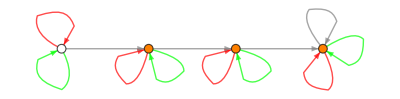

```mathematica
ShowStatePPM[growtreePPM,growtreePPMinit3]
```

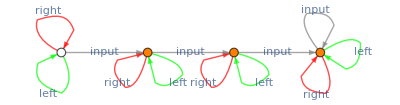

```mathematica
ShowStatePPM[growtreePPM,growtreePPMinit3,ShowEdgeState->True]
```

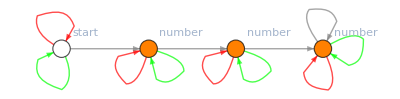

```mathematica
ShowStatePPM[growtreePPM,growtreePPMinit3,ShowNodeState->True,NodeSize->Medium]
```

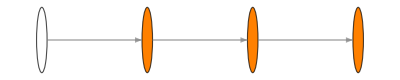

```mathematica
ShowStatePPM[growtreePPM,growtreePPMinit3,ShowEdgeLoops->False]
```

```mathematica
ClearAll[OneStepPPM,SELF,NEW,NodeColors,EdgeColors];
RuleOptionsPPM[rules_,state_,node_]:=Module[{alloptions,edgestates,circumstances},
edgestates=Complement[Keys[state[node]],{SELF}];
alloptions=Complement[Keys[rules],{NodeColors,EdgeColors}];
circumstances=Table[{state[node][SELF],edgestate,state[state[node][edgestate]][SELF]},{edgestate,edgestates}];
Do[If[state[node][edgestate]==node,AppendTo[circumstances,{state[node][SELF],edgestate,SELF}]],{edgestate,edgestates}];
Intersection[alloptions,circumstances]
]
SetAttributes[OneStepPPM,HoldRest];
OneStepPPM[rules_,state_]:=Module[{nodes=Keys[state],node,ruleoptions,nodecolor,edgecolor,readnodecolor,newnodecolor,newreadnodecolor,changedpointer,destinationspec,destination},
(* find a node that can take an action, if one exists -- list the possible actions *)
While[Length[nodes]>0 ,
node=RandomChoice[nodes]; nodes=Complement[nodes,{node}];
ruleoptions=RuleOptionsPPM[rules,state,node]; If[Length[ruleoptions]>0,Break[]];
];
If[Length[ruleoptions]==0,Return[False]];
(* look up the details for the rule *)
{nodecolor,edgecolor,readnodecolor}=RandomChoice[ruleoptions];
{{newnodecolor,newreadnodecolor},changedpointer,destinationspec}=rules[{nodecolor,edgecolor,readnodecolor}];
(* change node states for self and the read node, if applicable *)
state[node][SELF]=newnodecolor;If[!readnodecolor===SELF,state[state[node][edgecolor]][SELF]=newreadnodecolor];
(* reroute the designated edge pointer to either a new node or the node pointed to by a list of edges *)
If[MatchQ[destinationspec,_NEW],
destination=Max[Keys[state]]+1;
state[destination]=<|SELF->destinationspec[[1]],Table[edgecolor->destination,{edgecolor,Complement[Keys[state[node]],{SELF}]}]|>;
state[destination][destinationspec[[2]]]=node,
(* else *)
destination=Fold[state[#1][#2]&,node,destinationspec];
];
state[node][changedpointer]=destination;
Return[True];
]
```

```mathematica
RuleOptionsPPM[growtreePPM,growtreePPMinit3,4]
```

{{start,input,number}}

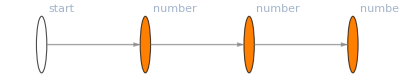

```mathematica
growtreePPMstate=growtreePPMinit3;ShowStatePPM[growtreePPM,growtreePPMstate,ShowNodeState->True,ShowEdgeLoops->False]
```

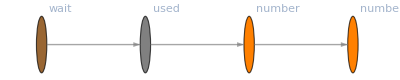

```mathematica
OneStepPPM[growtreePPM,growtreePPMstate];ShowStatePPM[growtreePPM,growtreePPMstate,ShowNodeState->True,ShowEdgeLoops->False]
```

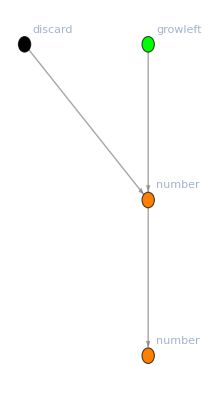

```mathematica
OneStepPPM[growtreePPM,growtreePPMstate];ShowStatePPM[growtreePPM,growtreePPMstate,ShowNodeState->True,ShowEdgeLoops->False]
```

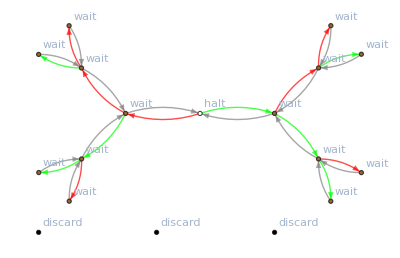

```mathematica
growtreePPMstate=growtreePPMinit3;While[OneStepPPM[growtreePPM,growtreePPMstate]];ShowStatePPM[growtreePPM,growtreePPMstate,ShowNodeState->True,ShowEdgeLoops->False]
```

```mathematica
growtreePPMstate=With[{d=7},<| Table[i-><|SELF->number,input->Max[1,i-1],left->i,right->i|>,{i,1,d}]~Join~{(d+1)-><|SELF->start,input->d,left->d+1,right->d+1|>}|>];
While[OneStepPPM[growtreePPM,growtreePPMstate]];ShowStatePPM[growtreePPM,growtreePPMstate,ShowNodeState->False,ShowEdgeLoops->False]
```

-Graphics-

Fun facts:  
	1. Like L-systems, our parallel pointer machines can grow exponentially large in linear time.  (What is “time” for an asynchronous parallel model?  If at a given moment there are K rules that could apply, and we imagine them each having a uniform independent probability of occurring at any instant, then the next event will occur in expected time O(1/K).)  However, unlike L-systems, parallel pointer machines can also communicate quickly from any node to any other node if they set up their topology appropriately.   They can therefore solve exponentially-hard problems in linear time (admittedly, using exponential resources in terms of the number of active nodes).
	2. Stephen Wolfram and others are exploring very simple types of graph rewriting systems as a potential algorithmic foundation for fundamental physics.

## Graph Rewriting Grammars

This is based on Klavins, Ghrist, Lipsky (2006) “A Grammatical Approach to Self-Organizing Robotic Systems”, although it is not identical as we allow the graph to grow or shrink in addition to changing vertex state and connectivity.

The state of the system will be a graph with annotations labels for the vertices, indicating the state of each vertex.  The set of vertices and the set of labels must be disjoint, which we will achieve by requiring vertices be integers and labels be non-integers.

The grammar rules (“reactions”) will consist of a pair of labeled graphs, each containing 1, 2, or 3 vertices.   A rule is applicable if the LHS graph appears (renamed) as a subgraph of the system state graph, with identical labels.  To apply the rule: 
	(0) Edges between vertices in the LHS are removed from the system state graph.
	(1) Any vertices in the LHS that are not in the RHS are removed (along with associated edges and labels).
	(2) Vertices in the RHS that are not in LHS are added.
	(3) The labels for vertices that are in both the RHS and the LHS are updated to match the RHS, and labels for new vertices are added.
	(4) Edges between vertices in the RHS are added.

If we attempt to apply a rule in a place where it is not applicable, the original system state graph will be returned unchanged; otherwise, the updated graph is returned.

```mathematica
ApplyGraphRule[G_,Rule[LHS_,RHS_],vertices_]:=Module[{sG=Subgraph[G,vertices],mapping=MapThread[Rule,{VertexList[LHS],vertices}]},
If[VertexCount[LHS]!=VertexCount[sG] || 
(vertices/.AnnotationValue[G,VertexLabels])=!= (VertexList[LHS]/.AnnotationValue[LHS,VertexLabels])||
(Sort/@EdgeList[sG])=!=(Sort/@(EdgeList[LHS]/.mapping)),
G, (* not applicable *)
nG=EdgeDelete[G,EdgeList[LHS]/.mapping];
nG=VertexDelete[nG,Complement[VertexList[LHS],VertexList[RHS]]/.mapping];
newvertices=Complement[VertexList[RHS],VertexList[LHS]];
newmapping=mapping~Join~MapThread[Rule,{newvertices,Max[VertexList[G]]+Range[Length[newvertices]]}];
nG=VertexAdd[nG,newvertices/.newmapping];
nG=Fold[Annotate[{#1,#2[[1]]},VertexLabels->#2[[2]]]&,nG,Transpose[{VertexList[RHS]/.newmapping,VertexList[RHS]/.AnnotationValue[RHS,VertexLabels]}]];
nG=EdgeAdd[nG,EdgeList[RHS]/.newmapping];
nG]
]
```

```mathematica
Clear[a,b,c]; (* These rules link up a's into chains and cycles. *)
Phi1={
Graph[{1,2},{},VertexLabels->{1->a,2->a}]->Graph[{1,2},{1<->2},VertexLabels->{1->b,2->b}],
Graph[{1,2},{},VertexLabels->{1->a,2->b}]->Graph[{1,2},{1<->2},VertexLabels->{1->b,2->c}],
Graph[{1,2},{},VertexLabels->{1->b,2->b}]->Graph[{1,2},{1<->2},VertexLabels->{1->c,2->c}]
}
```

```mathematica
Phi1graph=Graph[Range[9],{},VertexLabels->MapThread[Rule,{Range[9],Table[a,9]}]]
```

```mathematica
ApplyGraphRule[Phi1graph,Phi1[[1]],{1,5}]
```

Our super-inefficient simulator will choose triples at random and try to apply random rules to them.  We are too lazy to write a function that determines when there are no more applicable rules, so we’ll just do it for a while...

```mathematica
GraphGrammarSteps[G_,rules_,steps_]:=Module[{n=VertexCount[G],state=G},
Do[
With[{rule=RandomChoice[rules]},
state=ApplyGraphRule[state,rule,RandomSample[VertexList[state],VertexCount[First[rule]]]]],
steps];
state
]
```

```mathematica
GraphGrammarSteps[Phi1graph,Phi1,100]
```

```mathematica
Clear[a,b,c,d,e,f,g,h]; (* These rules create a unidirectional "walker" on a chain. *)
Phi3={
Graph[{1,2},{1<->2},VertexLabels->{1->a,2->c}]->Graph[{1,2},{},VertexLabels->{1->d,2->e}],
Graph[{1,2,3},{1<->2,2<->3},VertexLabels->{1->e,2->b,3->g}]->Graph[{1,2,3},{1<->2,2<->3,1<->3},VertexLabels->{1->c,2->b,3->h}],
Graph[{1,2},{1<->2},VertexLabels->{1->b,2->h}]->Graph[{1,2},{1<->2},VertexLabels->{1->f,2->b}],
Graph[{1,2},{1<->2},VertexLabels->{1->d,2->f}]->Graph[{1,2},{1<->2},VertexLabels->{1->g,2->a}]
};
Phi3//MatrixForm 
(* WARNING: The graphs aren't always displayed with the expected order of vertices so the correspondence should be determined from the text *)
```

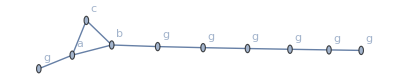

```mathematica
Phi3graph=Graph[Range[10],Table[i<->i+1,{i,1,8}]~Join~{2<->10,3<->10},VertexLabels->MapThread[Rule,{Range[10],{g,a,b,g,g,g,g,g,g,c}}]]
```

```mathematica
Dynamic[Phi3graph]
```

```mathematica
Do[Phi3graph=GraphGrammarSteps[Phi3graph,Phi3,100],100]
```

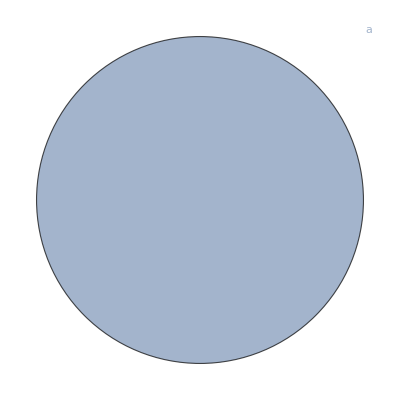
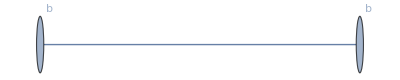
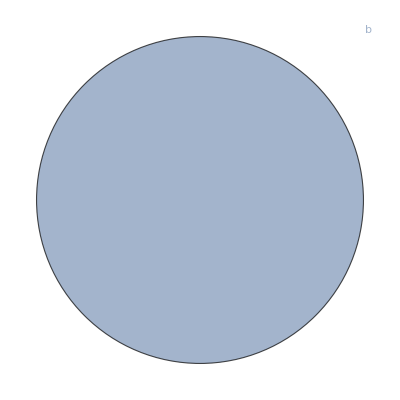
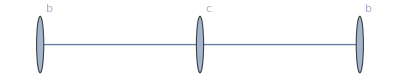
(-Graphics-→-Graphics-
-Graphics-→-Graphics-)

```mathematica
Clear[a,b,c]; (* These rules create an ever-growing binary tree. *)
PhiT={
Graph[{1},{},VertexLabels->{1->a}]->Graph[{1,2},{1<->2},VertexLabels->{1->b,2->b}],
Graph[{1},{},VertexLabels->{1->b}]->Graph[{1,2,3},{1<->2,1<->3},VertexLabels->{1->c,2->b,3->b}]
};
PhiT//MatrixForm
```

```mathematica
PhiTgraph=Graph[{1},{},VertexLabels->{1->a}];
```

```mathematica
Dynamic[PhiTgraph]
```

```mathematica
Do[PhiTgraph=GraphGrammarSteps[PhiTgraph,PhiT,1],100]
```

Challenge:  Can you design a set of graph grammar rule, with O(k) rules and O(k) label types, that grows into square grid of size O(2^k) when started with a single node?

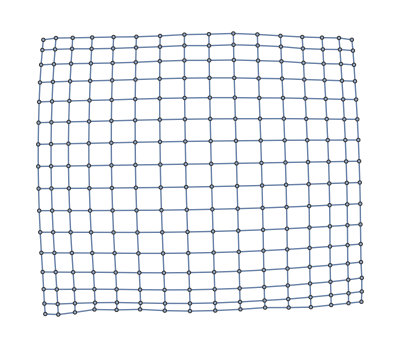

```mathematica
gr=With[{N=16},Graph[Union[Flatten[Table[Sort/@
{If[i>1,{i,j}<->{i-1,j},{}],
If[j>1,{i,j}<->{i,j-1},{}],
If[i<N,{i,j}<->{i+1,j},{}],
If[j<N,{i,j}<->{i,j+1},{}]},
{i,1,N},{j,1,N}]]],
AnnotationRules->Flatten[Table[{i,j}->{"color"->If[Mod[i+j,2]==0,Red,Blue]},{i,1,N},{j,1,N}]]
]]
```

Fun facts:  
	1. Starting with an initial linear graph, this graph grammar model can simulate Turing machines directly.  
	2. Starting with an initial lattice graph, this graph grammar model can simulate cellular automata using a synchronization mechanism.  And by growing the graph as needed, it can simulate an infinite cellular automaton running from a finite initial condition.
	3. With a suitable notion of parallel time (i.e. events happen at a fixed rate per node), this model can grow exponentially large graphs in linear time.